```mathematica
(*Justin Jobin, Rebecca Abi Abdallah, Hervé Guimond, Sandrine Leduc*)
```

1. Générer les fonctions rho(x) et g1(x) qui interpolent les données de l’article

a. altitudes h (converties en mètres, facteur 0.3048)

```mathematica
altitude=(Range[11]*5000+75000)*0.3048;
```

b. données sur rho (table de l’article, il semble y avoir une erreur dans l’article avec 2 coefficients intervertis ?, corrigé ici)

```mathematica
rhodata={0.044173,0.034754,0.027391,0.021187,0.017102,0.01647,0.013547,0.0083956,0.006487,0.0052871,0.004213};
```

c. données sur g1 (table de l’article), à multiplier par g à altitude 0 = 9.8065 (m/s^2)

```mathematica
g=9.8065;
g1data=g*{0.9924,0.9919,0.9914,0.9910,0.9905,0.99,0.9895,0.9891,0.9886,0.9881,0.9876};
```

d. utiliser la commande d’interpolation pour créer les fonctions rho[x] et g1[x]

```mathematica
rho=Interpolation[Transpose[{altitude,rhodata}]];
```

```mathematica
g1=Interpolation[Transpose[{altitude,g1data}]];
```

```mathematica
(*Création des moyennes de Rho et de g1 pour les solutions 1 et 2*)
moyenneRho=Mean[{0.044173,0.034754,0.027391,0.021187,0.017102,0.01647,0.013547,0.0083956,0.006487,0.0052871,0.004213}];
moyenneg1=Mean[g*{0.9924,0.9919,0.9914,0.9910,0.9905,0.99,0.9895,0.9891,0.9886,0.9881,0.9876}];
```

```mathematica
(*Voici tous les paramètres du modèle
-> a et c sont des coefficients de la force de traînée
-> x0 est l'altitude du sauteur au départ
-> tfinal est le temps final du saut
-> m est la masse du sauteur*)
a=1;
c=0.932;
x0=39600;tfinal=80 ;m=100;
```

```mathematica
(*La solution 2, on résout le problème avec rho et g1 comme des constantes.*)
{x2,v2}=DSolveValue[{x2'[t]==v2[t],v2'[t]==-moyenneg1+(0.5*moyenneRho*c*a*v2[t]^2)/m,v2[0]==0,x2[0]==x0},{x2,v2},{t,0,tfinal}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 2129818723 Log[ⅇ^(678.697 1)] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{Function[{t},47821.8+339.349 t-11861.5 Log[1.+ⅇ^(0.0572186 t)]],Function[{t},(339.349-339.349 ⅇ^(0.0572186 t))/(1.+1. ⅇ^(0.0572186 t))]}

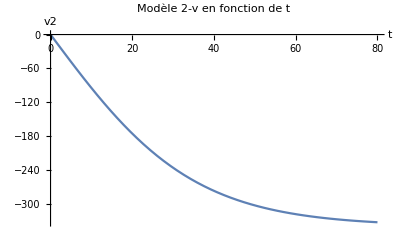

```mathematica
(*Le graphique de la solution 2 de la vitesse en fonction du temps.*)
Plot[v2[t],{t,0,tfinal},AxesLabel->{HoldForm[t],HoldForm[v2]},PlotLabel->HoldForm[Modèle 2-v en fonction de t],LabelStyle->{12,GrayLevel[0]}]
```

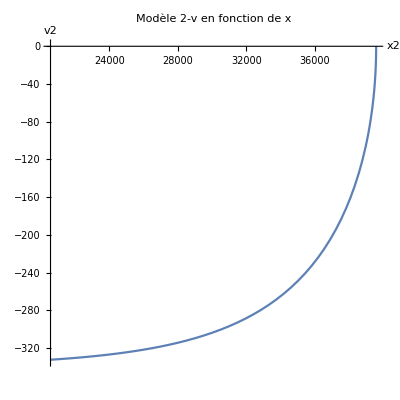

```mathematica
(*Le graphique de la solution 2 de la vitesse en fonction de l'altitude du sauteur.*)
ParametricPlot[{x2[t],v2[t]},{t,0,tfinal},AspectRatio->1,AxesLabel->{HoldForm[x2],HoldForm[v2]},PlotLabel->HoldForm[Modèle 2-v en fonction de x],LabelStyle->{12,GrayLevel[0]}]
```

3. Essayer de résoudre exactement le modèle dans la version 3 (coefficients variables)

Il faudra remplacer les ... par les bons termes

```mathematica
(*Voici la solution 3 présenté de manière exacte et non numérique.*)
{x3ex,v3ex}=DSolveValue[{x3ex'[t]==v3ex[t] ,v3ex'[t]==-g1[x3ex[t]]+(0.5*rho[x3ex[t]]*c*a*v3ex[t]^2)/m,x3ex[0]==x0,v[0]==0},{x3ex[t],v3ex[t]},{t,0,tfinal}]
```

DSolveValue::deqx: Supplied equations are not differential or integral equations of the given functions.

Set::shape: Lists {x3ex,v3ex} and DSolveValue[{x3ex'[t]==v3ex[t],v3ex'[t]==0.00466 v3ex[t]^2 InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«11»}},{Developer`PackedArrayForm,{«12»},{«11»}},{Automatic}][x3ex[t]]-InterpolatingFunction[{{«2»}},{5,7,0,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«11»}},{Developer`PackedArrayForm,{«12»},{«11»}},{Automatic}][x3ex[t]],x3ex[0]==39600,v[0]==0},{x3ex[t],v3ex[t]},{t,0,80}] are not the same shape.

DSolveValue[{x3ex'[t]==v3ex[t],v3ex'[t]==0.00466 v3ex[t]^2 InterpolatingFunction[…][x3ex[t]]-InterpolatingFunction[…][x3ex[t]],x3ex[0]==39600,v[0]==0},{x3ex[t],v3ex[t]},{t,0,80}]

Bref ... Mathematica n’est pas capable de résoudre le problème exactement quand rho et g1 dépendent de x. Mais si on les remplace par des valeurs qui ne dépendent pas de x, cela devrait fonctionner ! À essayer !!

4. Résoudre numériquement le modèle dans la version 3 (coefficients variables)

```mathematica
(*Voici la solution 3 présenté de manière numérique, c'est celle-ci qui sera présenté dans le graphique.*)
{x3,v3}=NDSolveValue[{x3'[t]==v3[t] ,v3'[t]==-g1[x3[t]]+(0.5*rho[x3[t]]*c*a*v3[t]^2)/m,x3[0]==x0,v3[0]==0},{x3,v3},{t,0,tfinal}]
```

NDSolveValue::deqn: Equation or list of equations expected instead of True in the first argument {«1»}.

Set::shape: Lists {x3,v3} and «1» are not the same shape.

NDSolveValue[{InterpolatingFunction[…][t]==InterpolatingFunction[…][t],InterpolatingFunction[…][t]==0.00466 (InterpolatingFunction[…][t])^2 InterpolatingFunction[…][InterpolatingFunction[…][t]]-InterpolatingFunction[…][InterpolatingFunction[…][t]],True,True},{InterpolatingFunction[…],InterpolatingFunction[…]},{t,0,80}]

5. Graphiques et recherche du maximum de vitesse

Graphique de la vitesse vers le bas en fonction de t

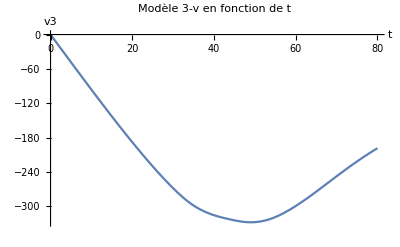

```mathematica
Plot[v3[t],{t,0,tfinal},AxesLabel->{HoldForm[t],HoldForm[v3]},PlotLabel->HoldForm[Modèle 3-v en fonction de t],LabelStyle->{12,GrayLevel[0]}]
```

Graphique de la vitesse vers le bas en fonction de x

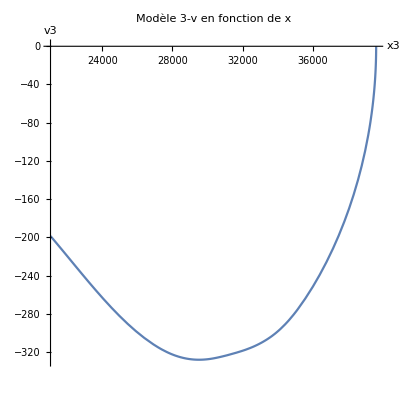

```mathematica
ParametricPlot[{x3[t],v3[t]},{t,0,tfinal},AspectRatio->1,AxesLabel->{HoldForm[x3],HoldForm[v3]},PlotLabel->HoldForm[Modèle 3-v en fonction de x],LabelStyle->{12,GrayLevel[0]}]
```

Trouver le maximum de la vitesse vers le bas (et convertir en km/h, donc facteur 3.6)

```mathematica
(*Le maximum de la vitesse vers le bas pour la solution 3.*)
{v3max,t3max}=FindMaximum[-3.6*v3[t],{t,40,0,80}]
```

{1180.9,{t→49.0166}}

```mathematica
(*L'altitude à la vitesse maximale vers le bas de la soltuion 3.*)
x3[t/.t3max]
```

29513.

```mathematica
(*Le maximum de la vitesse vers le bas pour la solution 2.*)
{v2max,t2max}=FindMaximum[-3.6*v2[t],{t,40,0,80}]
```

FindMinimum::reged: The point {80.} is at the edge of the search region {0.,80.} in coordinate 1 and the computed search direction points outside the region.

{1196.79,{t→80.}}

```mathematica
(*L'altitude à la vitesse maximale vers le bas de la soltuion 2.*)
x2[t/.t2max]
```

20552.5

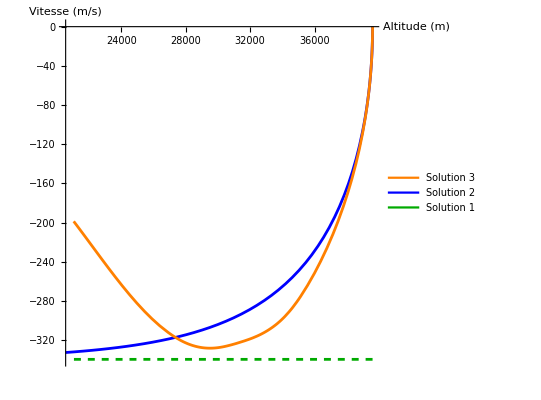
-Graphics-Vitesse en fonction de l'altitude

```mathematica
(*Voici le graphique présentant les trois solutions.*)
Labeled[ParametricPlot[{{x2[t],v2[t]},{x3[t],v3[t]},{x3[t],-339.42},{23328,-339.42}},{t,0,tfinal},AspectRatio->1,AxesLabel->{"Altitude (m)","Vitesse (m/s)"},PlotLegends->LineLegend[{Orange,Blue,Darker[Green]},{"Solution 3","Solution 2","Solution 1"} ],PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Orange},{Thickness[0.005],Dashed,Darker[Green]},{Thickness[0.02],Darker[Green]}}],"Vitesse en fonction de l'altitude"]
```